### Estimation parameters

```mathematica
capN=10
m=3
```

10

3

### Recursion for the coefficients of the integer valued polynomials

```mathematica
q[0]:=1;
q[s_]:=Product[x-k,{k,1,s}]/Factorial[s];
```

```mathematica
q[0,0]:=1;
q[0,m_]:=0;
q[s_,k_]:=q[s-1,k-1]/s- q[s-1,k];
```

```mathematica
q[0,0]
q[0,10]
q[0,-1]
q[7,1]
Table[q[s,k],{s,0,5},{k,0,5}] //MatrixForm
Expand[q[0]]
Expand[q[1]]
Expand[q[2]]
Expand[q[3]]
Expand[q[4]]
Expand[q[5]]
```

1

0

0

363/140

(1 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0
1 | -3/2 | 1/2 | 0 | 0 | 0
-1 | 11/6 | -1 | 1/6 | 0 | 0
1 | -25/12 | 35/24 | -5/12 | 1/24 | 0
-1 | 137/60 | -15/8 | 17/24 | -1/8 | 1/120)

1

-1+x

1-(3 x)/2+x^2/2

-1+(11 x)/6-x^2+x^3/6

1-(25 x)/12+(35 x^2)/24-(5 x^3)/12+x^4/24

-1+(137 x)/60-(15 x^2)/8+(17 x^3)/24-x^4/8+x^5/120

### Coefficient of the discrete orthogonal polynomials

```mathematica
d[k_,capN_]:=Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s],{s,0,k}]
P[k_,i_,capN_]:=Sum[(-1)^(s+k)*Binomial[s+k,s]*Binomial[capN-s-1,capN-k-1]*q[s,i],{s,0,k}];
```

```mathematica
Table[P[k,i,capN],{k,0,5},{i,0,5}] //MatrixForm
Expand[d[0,capN]]
Expand[d[1,capN]]
Expand[d[2,capN]]
Expand[d[3,capN]]
Expand[d[4,capN]]
Expand[d[5,capN]]
```

(1 | 0 | 0 | 0 | 0 | 0
-11 | 2 | 0 | 0 | 0 | 0
66 | -33 | 3 | 0 | 0 | 0
-286 | 761/3 | -55 | 10/3 | 0 | 0
1001 | -3850/3 | 5635/12 | -385/6 | 35/12 | 0
-3003 | 24752/5 | -10395/4 | 581 | -231/4 | 21/10)

1

-11+2 x

66-33 x+3 x^2

-286+(761 x)/3-55 x^2+(10 x^3)/3

1001-(3850 x)/3+(5635 x^2)/12-(385 x^3)/6+(35 x^4)/12

-3003+(24752 x)/5-(10395 x^2)/4+581 x^3-(231 x^4)/4+(21 x^5)/10

### Cramer-Rao bounds

```mathematica
CRB[i_,snr_,capN_]:=Sum[P[k,i,capN]^2/Binomial[capN+k,2*k+1]/Binomial[2*k,k],{k,0,m}]/(2*snr);
CRBstdbasis[i_,snr_,capN_]:=1/(2 snr)Part[Inverse[Table[Sum[n^(j+k),{n,1,capN}],{j,0,m},{k,0,m}]],i+1,i+1];
ApproxCRB[i_,snr_,capN_]:=1/(2*capN^(2*i+1)*snr)*(1/(2*i+1)+(m+1)^2/(2*capN*(i+1)^2)-1/(2*capN))*((m+i+1)*Binomial[m+i,i]*Binomial[m,i])^2;
```

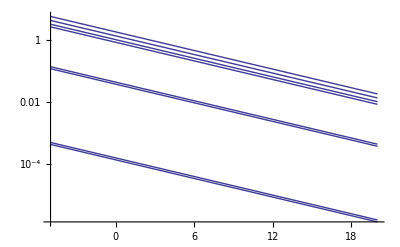

```mathematica
LogPlot[Flatten[Table[{CRB[i,10^(snrdb/10),capN],ApproxCRB[i,10^(snrdb/10),capN]},{i,0,m}]],{snrdb,-5,20}]
```

#### relative error between CRB and approximation

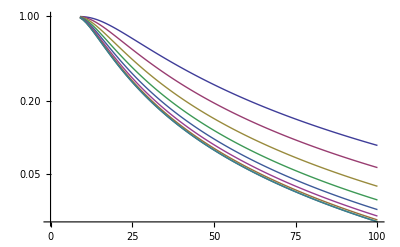

```mathematica
Needs["PlotLegends`"]
m=8;
snrdb=10;
CRBerror[i_,snr_,capN_] := (CRB[i,snr,capN]-ApproxCRB[i,snr,capN])/CRB[i,snr,capN];
plottable=Table[{capN,CRBerror[i,10^(snrdb/10),capN]},{i,0,m},{capN,m+1,100}];
ListLogPlot[plottable,PlotRange->{0,1.},PlotLegend->Table["i = "<>ToString[i],{i,0,m}],LegendPosition->{1.1,-0.4}, Joined->True]
```

Write the CRBs to a file

```mathematica
ToMetaPostString[v_] := ToString[NumberForm[v,ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row[{#1,"e",#3}]&)]];Do[fname = FileNameJoin[{NotebookDirectory[],"/data/crbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[CRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

```mathematica
Do[fname = FileNameJoin[{NotebookDirectory[],"/data/approxcrbN" <> ToString[capN] <> "m" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[snrdb]] <> "\t"  <> ToMetaPostString[N[ApproxCRB[i,10^(snrdb/10)]]]  "\n"],{snrdb,-5,25}];
Close[str];
,{i,0,m}]
```

Write relative errors to file

```mathematica
m=8;
snrdb=10;Do[fname = FileNameJoin[{NotebookDirectory[],"/data/relerrorm" <> ToString[m] <> "i" <> ToString[i]}];
str = OpenWrite[fname];
Do[WriteString[str, ToMetaPostString[N[capN]] <> "\t"  <> ToMetaPostString[N[CRBerror[i,10^(snrdb/10),capN]]]  "\n"],{capN,m+1,100}];
Close[str];
,{i,0,m}]
```